## Exercise 1. Importance of depth in ANNs to approximate functions.

The universal approximation theorem introduced in lectures shows that a linear layer followed by an activation function layer (i.e. a linear combination of activation functions) can accurately approximate any function if the layer is wide enough. According to this result, deep ANNs (i.e. ANNs with several layers) are not needed to approximate functions. In practice, however, the number of parameters required to approximate a certain function decreases if the depth of the ANN increases. This is an important motivation to use deep neural networks as opposed to shallow ANNs with a wide layer.

### Task 1

Follow the methods used in lecture’s section on the universal approximation theorem to generate data for the function f(x)=Cos(x) e^(-x/10) obtained by sampling N=5000 values of x in the interval [0,12]. Plot the data points {(x_i,f(x_i)),i=1,...,N} in a scatterplot.

### Task 2

In this task, you will train ANNs to approximate the function f(x). In particular, build three neural networks, ANN1, ANN2 and ANN3 consisting of linear layers followed by logistic sigmoid elementwise layers of decreasing width and increasing depth, as shown by the following summary graphics:

ANN1:

ANN2:

ANN3:

Note that the number of neurons is the same in the three networks. 

Train the three ANNs using the data created in Task 1. Compare the predictions of each trained ANN with f(x). Discuss the results.

## Exercise 2. Class net encoder for logistic regression for nominal classes

This exercise is related to the ANN for logistic regression presented in the lectures notebook Ch8-1 (section “Understanding ANNs through simple examples). Consider, in particular, the simple ANN called logistic2 in Ch8-1. The output variable of the ANN logistic2  was numeric even if logistic regression is a method that can be used for classification to any class that does not need to be numeric. In order to  consider a genuine nominal variable corresponding to, e.g., two classes A and B, one needs to add a “Class” net encoder (see Ch8-2_ML_NeuralNetworks_PartII.nb) to the ANN logistic2 defined in lectures. In addition, we append a SoftmaxLayer[] which normalizes the output of the logistic2 ANN in order to use it as class probabilities for classification tasks.

### Task 1

Following these ideas, build a neural net with the following structure:

-Graphics-

More explicitly, this can be obtained with NetChain and the appropriate layers as follows (I refer to the layer as logisticClass):

logisticClass = NetChain[{LAYERS},"Output"→NetDecoder[{"Class",{"A","B"}}]]

### Task 2

Display the summary graphic of logisticClass.

### Task 3

Use the following data to train logisticClass:

tDLogClass={1.2→”A”,2.1→”A”,3.4→”A”,5.1→”B”,7.3→ “B”,9.7→ “B”};

### Task 4

Show that the trained ANN predicts class A for input x≲4 and class B for x≳4.

## Exercise 3. Importance of non-linear activation layers to describe data

### Background

Non-linear activation functions such LogisticSigmoid, Tanh and Ramp described in lectures are at the core of the success of ANNs. Indeed, non-linear activation functions allow ANNs to be applied to complex datasets that cannot be dealt with by only using linear layers. For example, ANNs involving linear layers would be able to classify elements into two classes A and B in the following dataset:

The ultimate reason for the success of linear layers in this example is that the classes are linearly separable. In 2-dimensional data, this means that there exists at least one line that separates the clouds corresponding to different classes (in fact, in this example there are infinitely many straight lines that separate the classes). In contrast, non-linear layers are essential when data in different classes are not linearly separable. For example, non-linear activation functions are needed for classification in the following case:

This exercise explores the effect of non-linear activation layers for classification based on artificial neural networks.

### Task 1

Use the following function,

```mathematica
gaussian[μ_,σ_,n_]:=RandomVariate[MultinormalDistribution[μ,{{σ,0},{0,σ}}],n];
```

to generate data for two classes as follows:

100 data points for a class A obeying a multinormal distribution with μ=(0,0) and σ=0.05.

100 data points for a class B obeying a multinormal distribution with μ=(1,1) and σ=0.05.

Visualize the two classes with a scatterplot.

### Task 2

Build a neural net to classify points into classes A and B with a linear layer followed by a SoftmaxLayer and a class net decoder to transform the output of the SoftmaxLayer into classes A and B, as described in section 11.8.3. The ANN should have the following architecture:

### Task 3

Train the ANN built in Task 2 with the synthetic data defined in Task 1. Fix the maximum number of training rounds to 1000.

Use a scatterplot to compare the training data with the prediction of the trained ANN for points in and predicted classes by the ANN using a scatterplot. Check that the plot is similar to this one (of course, you are free to the colours you wish):

Remember that plots of this type were used, for instance, when explaining the

Predictions in this plot are obtained by applying the trained ANN to predict the class of points (x,y) in a rectangular domain [-1,2]×[-0.5,2]. The points in this region are separated by increments Δx = Δy=0.05 in the horizontal and vertical directions.

Hint: Inspiration on how to generate this plot can be obtained from section 5.1.1 in chapter 5. You could also use the function below:

```mathematica
plotClassification[xmin0_,xmax0_,ymin0_,ymax0_,Dx0_,Dy0_,net0_,classA0_,classB0_]:=Module[{xmin=xmin0,xmax=xmax0,ymin=ymin0,ymax=ymax0,Dx=Dx0,Dy=Dy0,net=net0,classA=classA0,classB=classB0},
linex=Range[xmin,xmax,Dx];
liney=Range[ymin,ymax,Dy];
points=Tuples[{linex,liney}];
pred=net[points];
temp=Tally[Sort[pred]];
Show[ListPlot[{points[[Ordering[pred]]][[1;;temp[[1,2]]]],points[[Ordering[pred]]][[temp[[1,2]]+1;;Length[pred]]]}, PlotStyle->{{RGBColor[0.97,1.,0.55],PointSize[0.015]},{RGBColor[0.5,1,0.5],PointSize[0.015]}},PlotLegends->{"Predicted A","Predicted B"}],ListPlot[{classA,classB},PlotStyle->Large, PlotLegends->{"A","B"}]]
]
```

### Task 4

Consider the following synthetic data for two classes A and B:

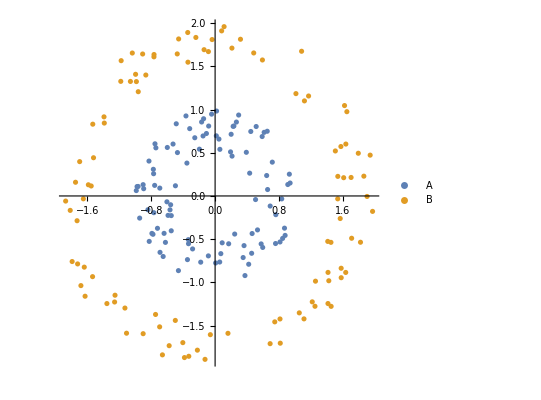

```mathematica
classA=RandomPoint[Annulus[{0,0},{0.5,1}],100];classB=RandomPoint[Annulus[{0,0},{1.5,2}],100];
ListPlot[{classA,classB},PlotLegends->{"A","B"},AspectRatio->1]
```

Use this data to train an ANN with the same architecture of the one built in Task 2.

Proceed as in Task 3 to do a scatterplot to compare the training data with prediction of the trained ANN for points in the domain [-2.5,2.5]×[-2.5,2.5]. The comparison should indicate that the trained ANN under-fits the data, i.e. the ANN lacks the capacity to describe the training data. Why is this the case?

### Task 5

To investigate the benefits of using non-linear activation layers for classification of non-linearly separable data, use NetChain to build a neural net with the following layers:

Train the ANN using the data created in Task 4 and do a scatterplot to compare the training data with prediction of the trained ANN for points in the domain [-2.5,2.5]×[-2.5,2.5]